{{9,61.9966},{12,129.136},{14,210.616},{16,343.431},{19,710.524},{21,1114.19}}

{{9,61.8557},{12,167.01},{14,265.979},{16,451.546},{19,822.68},{21,1088.66}}

{49.4845,68.0412,80.4124,98.9691,98.9691,117.526}

{{9,61.8557,49.4845},{12,167.01,68.0412},{14,265.979,80.4124},{16,451.546,98.9691},{19,822.68,98.9691},{21,1088.66,117.526}}

{{9,59.0301},{12,120.961},{14,195.142},{16,314.756},{19,641.297},{21,1000.1}}

{{9,61.8557},{12,117.526},{14,216.495},{16,383.505},{19,779.381},{21,1008.25}}

{30.9278,49.4845,49.4845,55.6701,74.2268,129.897}

{{9,61.8557,30.9278},{12,117.526,49.4845},{14,216.495,49.4845},{16,383.505,55.6701},{19,779.381,74.2268},{21,1008.25,129.897}}

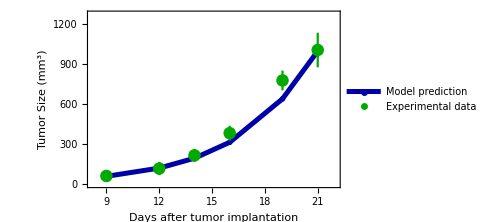

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.499407564865372;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;d2=0.0;
s=NDSolve[{T'[x]==(0.244597*T[x])/((1+(T[x]/1088.66)^μ)^(1/μ)),S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))* S[x]-(d+((d2*T[x])/(1+(T[x]/m2))))*M[x],T[0]==6.86,S[0]==252.5,M[0]==4797.08},{T,S,M},{x,0,100}];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
j1=(T[0]/.s)[[1]];j2=(T[5]/.s)[[1]];j3=(T[7]/.s)[[1]];j4=(T[9]/.s)[[1]];j5=(T[12]/.s)[[1]];j6=(T[14]/.s)[[1]];j7=(T[16]/.s)[[1]];j8=(T[19]/.s)[[1]];j9=(T[21]/.s)[[1]];j10=(T[23]/.s)[[1]];j11=(T[26]/.s)[[1]];j12=(T[28]/.s)[[1]];
j13=(T[30]/.s)[[1]];
j14=(T[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
data1=List[(*{0,j1},{5,j2},{7,j3},*){9,j4},{12,j5},{14,j6},{16,j7},{19,j8},{21,j9}(*,{23,j10},{26,j11},{28,j12}, {30,j13}, {33,j14} *)]
data2=Import["D:/datatumor.txt",{"Data",{All},{1,2}}]
error2=Import["D:/Errorbartumor.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error2}]
Needs["ErrorBarPlots`"]
G1=ListLinePlot[(*Split[data1,#2=!={0,0}&]*)data1,PlotMarkers->{Automatic,Medium},AxesStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"Model prediction"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.25,0.8}],PlotRange->{{8.2,22},{0,1275}},PlotStyle->{Darker[Blue],Thickness[0.01]}];
pl0=Show[G1,ErrorListPlot[withError,PlotStyle->{Red,PointSize[0.025]},PlotLegends->Placed[LineLegend[{"Experimental data"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.25,0.65}],ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Tumor Size (mm^3)",18(*,Bold*)]},FrameTicksStyle->Directive[Black,14],LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12]];
(*+++++++++++++++++++++++++++++++++++++++++++++++++++*)
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0.0;A2=0.89;A3=0.4;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[5]==22.68,S[5]==184.98,M[5]==4691.31},{T,S,M},{x,5,100}];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*jt1=(0.002*T[0]/.s)[[1]];*)
j2=(T[5]/.s)[[1]];j3=(T[7]/.s)[[1]];j4=(T[9]/.s)[[1]];j5=(T[12]/.s)[[1]];j6=(T[14]/.s)[[1]];j7=(T[16]/.s)[[1]];j8=(T[19]/.s)[[1]];j9=(T[21]/.s)[[1]];j10=(T[23]/.s)[[1]];j11=(T[26]/.s)[[1]];j12=(T[28]/.s)[[1]];
j13=(T[30]/.s)[[1]];
j14=(T[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
data1=List[(*{0,j1},{5,j2},{7,j3},*){9,j4},{12,j5},{14,j6},{16,j7},{19,j8},{21,j9}(*,{23,j10},{26,j11},{28,j12}, {30,j13}, {33,j14} *)]
data2=Import["D:/datatumor3.txt",{"Data",{All},{1,2}}]
error2=Import["D:/Errorbartumor2.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error2}]
Needs["ErrorBarPlots`"]
G2=ListLinePlot[(*Split[data1,#2=!={0,0}&]*)data1,PlotMarkers->{Automatic,Medium},AxesStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"Model prediction"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.25,0.8}],PlotRange->{{8.2,22},{0,1275}},PlotStyle->{Darker[Blue],Thickness[0.01]}];
pl00=Show[G2,ErrorListPlot[withError,PlotStyle->{Darker[Green],PointSize[0.025]},PlotLegends->Placed[LineLegend[{"Experimental data"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.25,0.65}],ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Tumor Size (mm^3)",18(*,Bold*)]},FrameTicksStyle->Directive[Black,14],LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12]]
(*++++++++++++++++++++++++++++++++++++++++++++++++++++*)
```

0.4

{{5,9.75258},{7,10.0657},{9,10.276},{12,10.4384},{14,10.4653},{16,10.4405},{19,10.3261},{21,10.2089},{23,10.0659},{26,9.81378},{28,9.62639},{30,9.42741},{33,9.11314}}

{{0,9.99223},{5,10.2139},{7,10.8089},{9,11.3686},{12,11.7067},{14,11.6785},{16,11.4649},{19,10.9707},{21,10.4066},{23,9.90646},{26,9.39526},{28,9.17663},{30,9.1489},{33,8.55804}}

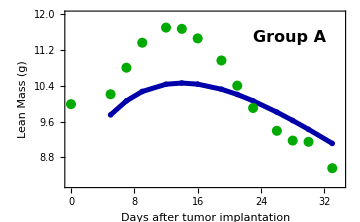

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0.0;A2=0.89;A3=0.4
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[5]==22.68,S[5]==184.98,M[5]==4691.31},{T,S,M},{x,5,100}];
(*jm1=(0.002*M[0]/.s)[[1]];*)
jm2=(0.002*M[5]/.s)[[1]];jm3=(0.002*M[7]/.s)[[1]];jm4=(0.002*M[9]/.s)[[1]];jm5=(0.002*M[12]/.s)[[1]];jm6=(0.002*M[14]/.s)[[1]];jm7=(0.002*M[16]/.s)[[1]];jm8=(0.002*M[19]/.s)[[1]];jm9=(0.002*M[21]/.s)[[1]];jm10=(0.002*M[23]/.s)[[1]];jm11=(0.002*M[26]/.s)[[1]];jm12=(0.002*M[28]/.s)[[1]];
jm13=(0.002*M[30]/.s)[[1]];
jm14=(0.002*M[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
(*js1=(0.002*S[0]/.s)[[1]];*)
js2=(0.002*S[5]/.s)[[1]];js3=(0.002*S[7]/.s)[[1]];js4=(0.002*S[9]/.s)[[1]];js5=(0.002*S[12]/.s)[[1]];js6=(0.002*S[14]/.s)[[1]];js7=(0.002*S[16]/.s)[[1]];js8=(0.002*S[19]/.s)[[1]];js9=(0.002*S[21]/.s)[[1]];js10=(0.002*S[23]/.s)[[1]];js11=(0.002*S[26]/.s)[[1]];js12=(0.002*S[28]/.s)[[1]];
js13=(0.002*S[30]/.s)[[1]];
js14=(0.002*S[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*jt1=(0.002*T[0]/.s)[[1]];*)
jt2=(0.002*T[5]/.s)[[1]];jt3=(0.002*T[7]/.s)[[1]];jt4=(0.002*T[9]/.s)[[1]];jt5=(0.002*T[12]/.s)[[1]];jt6=(0.002*T[14]/.s)[[1]];jt7=(0.002*T[16]/.s)[[1]];jt8=(0.002*T[19]/.s)[[1]];jt9=(0.002*T[21]/.s)[[1]];jt10=(0.002*T[23]/.s)[[1]];jt11=(0.002*T[26]/.s)[[1]];jt12=(0.002*T[28]/.s)[[1]];
jt13=(0.002*T[30]/.s)[[1]];
jt14=(0.002*T[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*j1=jm1+js1+jt1+14.988761408571424;*)
j2=jm2+js2;
j3=jm3+js3;
j4=jm4+js4;
j5=jm5+js5;
j6=jm6+js6;
j7=jm7+js7;
j8=jm8+js8;
j9=jm9+js9;
j10=jm10+js10;
j11=jm11+js11;
j12=jm12+js12;
j13=jm13+js13;
j14=jm14+js14;
data1=List[(*{0,j1},*){5,j2},{7,j3},{9,j4},{12,j5},{14,j6},{16,j7},{19,j8},{21,j9},{23,j10},{26,j11},{28,j12}, {30,j13}, {33,j14} ]
data2=Import["D:/green.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/greenerror.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
G1=ListLinePlot[(*Split[data1,#2=!={0,0}&]*)data1,PlotMarkers->{Automatic,Medium},AxesStyle->Directive[Black,12],(*PlotLegends->{"Model prediction"},*)PlotRange->{{-0.1,34},{8.2,12}},PlotStyle->{Darker[Blue],Thickness[0.01]}];
(*pl1=Show[G1,ErrorListPlot[withError,PlotStyle->Green,PlotLegends->{"Experimental data"},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{"Days after tumor implantation","Body weight (grams)"},FrameStyle->Directive[Black,12]]*)
pl1=Show[G1,ListPlot[data2,PlotStyle->{Darker[Green],PointSize[0.02]},(*PlotLegends->{"Experimental data"},*)ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},FrameStyle->Directive[Black,12],FrameTicksStyle->Directive[Black,14],(*PlotLabel->Style["Group A",14,Black,Bold]*)LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],Epilog->Text[Style["Group A",Black,Bold,Italic,16,FontFamily->"Times New Roman"],Scaled[{.8,.85}]]]
```

9.38261

0.369928

0.0453568

{{0,9.99248},{5,9.75254}}

{{0,9.99223},{5,10.2139},{7,10.8089},{9,11.3686},{12,11.7067},{14,11.6785},{16,11.4649},{19,10.9707},{21,10.4066},{23,9.90646},{26,9.39526},{28,9.17663},{30,9.1489},{33,8.55804}}

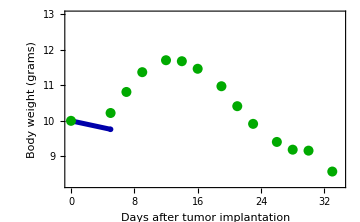

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s2=NDSolve[{TT'[x]-(0.239141*TT[x])/((1+(TT[x]/1008.25)^μ)^(1/μ))==0,SS'[x]==(2 *(P0+P1/(1+MM[x]/m))-1)* (v0+v1/(1+MM[x]/m)-(ϵ*TT[x]/(1+TT[x]/m2)))*SS[x]-((d1*TT[x])/(1+(TT[x]/m2)))*SS[x],MM'[x]==2 *(1-P0-P1/(1+MM[x]/m))*(v0+v1/(1+MM[x]/m)-(ϵ*TT[x]/(1+TT[x]/m2)))* SS[x]-d*MM[x],TT[0]==6.86,SS[0]==249.8,MM[0]==4746.44},{TT,SS,MM},{x,0,100}];
jmm1=(0.002*MM[0]/.s2)[[1]];
jmm2=(0.002*MM[5]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%*)
jss1=(0.002*SS[0]/.s2)[[1]];
jss2=(0.002*SS[5]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jtt1=(0.002*TT[0]/.s2)[[1]];
 jtt2=(0.002*TT[5]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jj1=jmm1+jss1;
jj2=jmm2+jss2;
data3=List[{0,jj1},{5,jj2}]
data4=Import["D:/green.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/greenerror.txt",{"Data",{All},{1}}]
withError=Transpose[{data4[[All,1]],data4[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
G2=ListLinePlot[(*Split[data3,#2=!={0,0}&]*)data3,PlotMarkers->{Automatic,Medium},AxesStyle->Directive[Black,12],(*PlotLegends->{"Model prediction"},*)PlotRange->{{-0.1,34},{8.2,13}},PlotStyle->{Darker[Blue],Thickness[0.01]}];
pl2=Show[G2,ListPlot[data4,PlotStyle->{Darker[Green],PointSize[0.02]},(*PlotLegends->{"Experimental data"},*)ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{"Days after tumor implantation","Body weight (grams)"},FrameStyle->Directive[Black,12]]
```

0.4

{{14,8.41788},{17,8.57978},{19,8.6251},{21,8.6296},{24,8.574},{26,8.50322},{28,8.41074},{31,8.23948},{33,8.10818},{35,7.96627},{38,7.73832},{40,7.57903}}

{{0,10.0033},{3,9.8724},{5,10.125},{7,10.0537},{10,10.0933},{12,9.87052},{14,9.35092},{17,8.49773},{19,8.30116},{21,8.26235},{24,8.13554},{26,7.65016},{28,7.76797},{31,7.57373},{33,7.3471},{35,7.21263},{38,7.10977},{40,6.84339}}

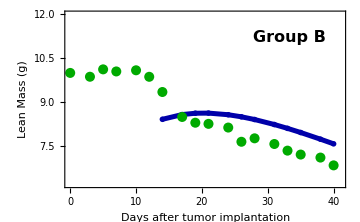

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0.0;A2=0.89;A3=0.4
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[14]==195.13,S[14]==106.939,M[14]==4102},{T,S,M},{x,14,100}];
(*jm1=(0.002*M[0]/.s)[[1]];
jm2=(0.002*M[3]/.s)[[1]];jm3=(0.002*M[5]/.s)[[1]];jm4=(0.002*M[7]/.s)[[1]];jm5=(0.002*M[10]/.s)[[1]];jm6=(0.002*M[12]/.s)[[1]];*)
jm7=(0.002*M[14]/.s)[[1]];jm8=(0.002*M[17]/.s)[[1]];jm9=(0.002*M[19]/.s)[[1]];jm10=(0.002*M[21]/.s)[[1]];jm11=(0.002*M[24]/.s)[[1]];jm12=(0.002*M[26]/.s)[[1]];jm13=(0.002*M[28]/.s)[[1]];
jm14=(0.002*M[31]/.s)[[1]];
jm15=(0.002*M[33]/.s)[[1]];
jm16=(0.002*M[35]/.s)[[1]];
jm17=(0.002*M[38]/.s)[[1]];
jm18=(0.002*M[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
(*js1=(0.002*S[0]/.s)[[1]];
js2=(0.002*S[3]/.s)[[1]];js3=(0.002*S[5]/.s)[[1]];js4=(0.002*S[7]/.s)[[1]];js5=(0.002*S[10]/.s)[[1]];js6=(0.002*S[12]/.s)[[1]];*)
js7=(0.002*S[14]/.s)[[1]];js8=(0.002*S[17]/.s)[[1]];js9=(0.002*S[19]/.s)[[1]];js10=(0.002*S[21]/.s)[[1]];js11=(0.002*S[24]/.s)[[1]];js12=(0.002*S[26]/.s)[[1]];js13=(0.002*S[28]/.s)[[1]];
js14=(0.002*S[31]/.s)[[1]];
js15=(0.002*S[33]/.s)[[1]];
js16=(0.002*S[35]/.s)[[1]];
js17=(0.002*S[38]/.s)[[1]];
js18=(0.002*S[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*jt1=(0.002*T[0]/.s)[[1]];
jt2=(0.002*T[3]/.s)[[1]];jt3=(0.002*T[5]/.s)[[1]];jt4=(0.002*T[7]/.s)[[1]];jt5=(0.002*T[10]/.s)[[1]];jt6=(0.002*T[12]/.s)[[1]];*)
jt7=(0.002*T[14]/.s)[[1]];jt8=(0.002*T[17]/.s)[[1]];jt9=(0.002*T[19]/.s)[[1]];jt10=(0.002*T[21]/.s)[[1]];jt11=(0.002*T[24]/.s)[[1]];jt12=(0.002*T[26]/.s)[[1]];jt13=(0.002*T[28]/.s)[[1]];
jt14=(0.002*T[31]/.s)[[1]];
jt15=(0.002*T[33]/.s)[[1]];
jt16=(0.002*T[35]/.s)[[1]];
jt17=(0.002*T[38]/.s)[[1]];
jt18=(0.002*T[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*j1=jm1+jss1+jtt1+15.005353690141742;j2=jm2+jss2+jtt2+14.82056023366874;j3=jmm3+jss3+jtt3+15.207334331475879;j4=jmm4+jss4+jtt4+15.113326656457652;j5=jmm5+jss5+jtt5+15.209507701028155;j6=jmm6+jss6+jtt6+14.920825278008387;*)
j7=jm7+js7;
j8=jm8+js8;
j9=jm9+js9;
j10=jm10+js10;
j11=jm11+js11;
j12=jm12+js12;
j13=jm13+js13;
j14= jm14+js14;
j15=jm15+js15;
j16=jm16+js16;
j17=jm17+js17;
j18=jm18+js18;
data1=List[(*{0,j1},{3,j2},{5,j3},{7,j4},{10,j5},{12,j6},*){14,j7},{17,j8},{19,j9},{21,j10},{24,j11},{26,j12},{28,j13},{31,j14}, {33,j15},{35,j16},{38,j17},{40,j18}]
data2=Import["D:/green2.txt",{"Data",{All},{1,2}}]
G3=ListLinePlot[(*Split[data1,#2=!={0,0}&]*)data1,PlotMarkers->{Automatic,Medium},AxesStyle->Directive[Black,12],(*PlotLegends->{"Model prediction"},*)PlotRange->{{0,41},{6.2,12}},PlotStyle->{Darker[Blue],Thickness[0.01]}];
pl3=Show[G3,ListPlot[data2,PlotStyle->{Darker[Green],PointSize[0.02]},(*PlotLegends->{"Experimental data"},*)ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},FrameStyle->Directive[Black,12],FrameTicksStyle->Directive[Black,14],LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],(*PlotLabel->Style["Group B",14,Black,Bold]*)FrameStyle->Directive[Black,12],Epilog->Text[Style["Group B",Black,Bold,Italic,16,FontFamily->"Times New Roman"],Scaled[{.8,.85}]]]
```

8.204

0.213878

0.390255

{{0,10.0017},{3,9.9277},{5,9.76014},{7,9.52575},{10,9.0888},{12,8.76136},{14,8.41788}}

{{0,10.0033},{3,9.8724},{5,10.125},{7,10.0537},{10,10.0933},{12,9.87052},{14,9.35092},{17,8.49773},{19,8.30116},{21,8.26235},{24,8.13554},{26,7.65016},{28,7.76797},{31,7.57373},{33,7.3471},{35,7.21263},{38,7.10977},{40,6.84339}}

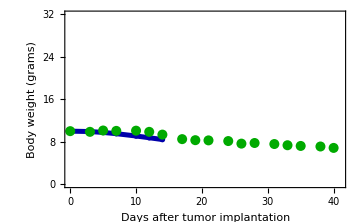

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s2=NDSolve[{TT'[x]-(0.239141*TT[x])/((1+(TT[x]/1008.25)^μ)^(1/μ))==0,SS'[x]==(2 *(P0+P1/(1+MM[x]/m))-1)* (v0+v1/(1+MM[x]/m)-(ϵ*TT[x]/(1+TT[x]/m2)))*SS[x]-((d1*TT[x])/(1+(TT[x]/m2)))*SS[x],MM'[x]==2 *(1-P0-P1/(1+MM[x]/m))*(v0+v1/(1+MM[x]/m)-(ϵ*TT[x]/(1+TT[x]/m2)))* SS[x]-d*MM[x],TT[0]==6.86,SS[0]==250.042,MM[0]==4750.8},{TT,SS,MM},{x,0,100}];
jmm1=(0.002*MM[0]/.s2)[[1]];
jmm2=(0.002*MM[3]/.s2)[[1]];
jmm3=(0.002*MM[5]/.s2)[[1]];
jmm4=(0.002*MM[7]/.s2)[[1]];
jmm5=(0.002*MM[10]/.s2)[[1]];
jmm6=(0.002*MM[12]/.s2)[[1]];
jmm7=(0.002*MM[14]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%*)
jss1=(0.002*SS[0]/.s2)[[1]];
jss2=(0.002*SS[3]/.s2)[[1]];
jss3=(0.002*SS[5]/.s2)[[1]];
jss4=(0.002*SS[7]/.s2)[[1]];
jss5=(0.002*SS[10]/.s2)[[1]];
jss6=(0.002*SS[12]/.s2)[[1]];
jss7=(0.002*SS[14]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jtt1=(0.002*TT[0]/.s2)[[1]];
jtt2=(0.002*TT[3]/.s2)[[1]];
jtt3=(0.002*TT[5]/.s2)[[1]];
jtt4=(0.002*TT[7]/.s2)[[1]];
jtt5=(0.002*TT[10]/.s2)[[1]];
jtt6=(0.002*TT[12]/.s2)[[1]];
jtt7=(0.002*TT[14]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jj1=jmm1+jss1;
jj2=jmm2+jss2;
jj3=jmm3+jss3;
jj4=jmm4+jss4;
jj5=jmm5+jss5;
jj6=jmm6+jss6;
jj7=jmm7+jss7;
data3=List[{0,jj1},{3,jj2},{5,jj3},{7,jj4},{10,jj5},{12,jj6},{14,jj7}]
data4=Import["D:/green2.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/greenerror2.txt",{"Data",{All},{1}}]
withError=Transpose[{data4[[All,1]],data4[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
G4=ListLinePlot[(*Split[data3,#2=!={0,0}&]*)data3,PlotMarkers->{Automatic,Medium},AxesStyle->Directive[Black,12],(*PlotLegends->{"Model prediction"},*)PlotRange->{{0,41},{0,32}},PlotStyle->{Darker[Blue],Thickness[0.01]}];
(*pl2=Show[G2,ErrorListPlot[withError,PlotStyle->Green,PlotLegends->{"Experimental data"},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{"Days after tumor implantation","Body weight (grams)"},FrameStyle->Directive[Black,12]]*)
pl4=Show[G4,ListPlot[data4,PlotStyle->{Darker[Green],PointSize[0.02]},(*PlotLegends->{"Experimental data"},*)ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{"Days after tumor implantation","Body weight (grams)"},FrameStyle->Directive[Black,12]]
```

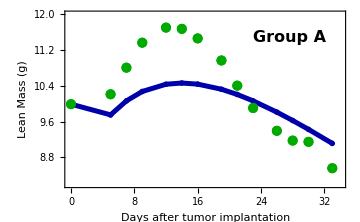

```mathematica
fig1=Show[pl1,pl2]
```

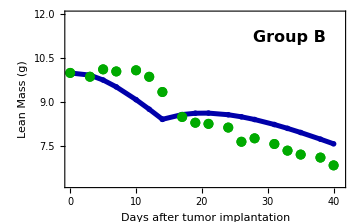

```mathematica
fig2=Show[pl3,pl4]
```

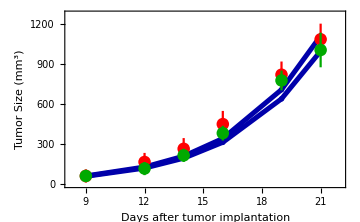

```mathematica
fig3=Show[pl0,pl00]
```

```mathematica
(*Grid[fig1,fig2,fig3]*)
```

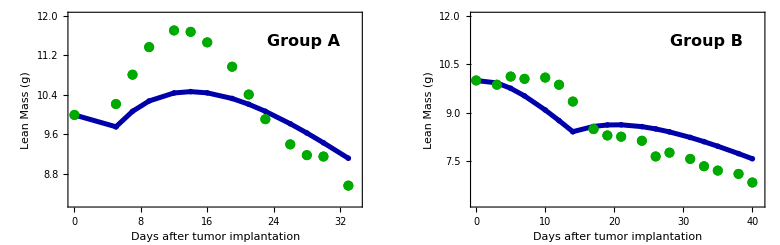

```mathematica
d1=GraphicsGrid[{{fig1,fig2}}]
```

```mathematica
ff=GraphicsGrid[{{d1},{pl00}}]
```

-Graphics-

```mathematica
Export["D:/TTT4.eps",ff]
```

D:/TTT4.eps

```mathematica
"D:/TTT.eps"
```

D:/TTT.eps

```mathematica
Export["D:/TTT1.eps",pl0]
```

D:/TTT1.eps